```mathematica
Manipulate[Graphics[ArrayPlot[CellularAutomaton[60,{{1},0},t]], PlotRange->{{-100,100}, {0,100}}], {t, 0, 30, 1}]
```

```mathematica
g=Table[Graphics[ArrayPlot[CellularAutomaton[60,{{1},0},t]], PlotRange->{{-100,100}, {0,100}}], {t, 0, 30, 1}];
SetDirectory@NotebookDirectory[];
Export["CellAutomaton_Rule_60.gif",g]
```

CellAutomaton_Rule_60.gif

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["CellAutomaton_Rule_60.gif"]]]
```

```mathematica
RulePlot[CellularAutomaton[60]]
```

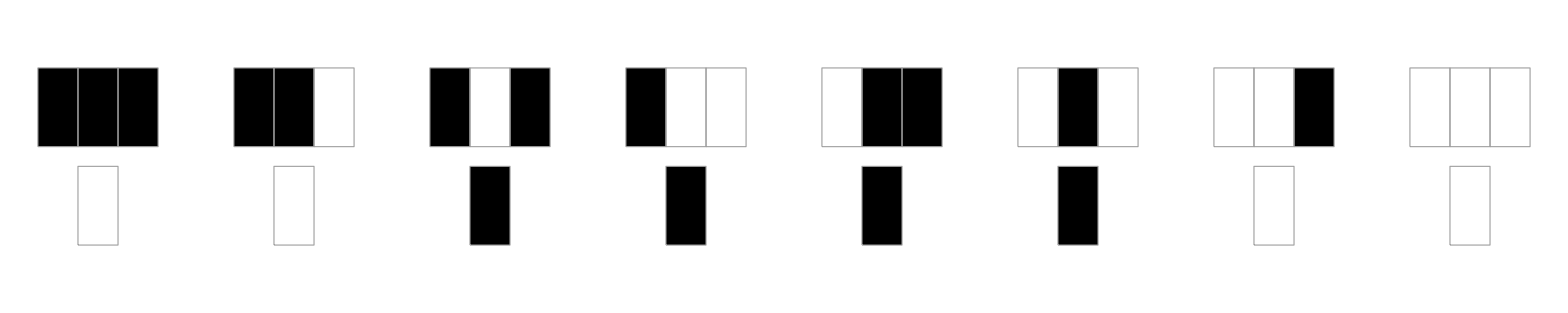

```mathematica
gameOfLife={224,{2,{{2,2,2},{2,1,2},{2,2,2}}},{1,1}};
board=RandomInteger[1,{50,50}];
Dynamic[ArrayPlot[board=Last[CellularAutomaton[gameOfLife,board,{{0,1}}]]]]
(*g = Table[ArrayPlot[board=Last[CellularAutomaton[gameOfLife,board,t]]], {t, 0, 100, 1}];
SetDirectory@NotebookDirectory[];
Export["gameoflife.gif",g, "DisplayDurations"->0.3]*)
```

gameoflife.gif